```mathematica
para[a_,b_]:=para[a,b]=(a b)/(a+b);
M=10^6;
u=10^-6;
k=10^3;
n=10^-9;
```

```mathematica
R13=3.3M;
C8=10u;
C6=10u;
C7=15n;
R11=91k;
R10=820k;
```

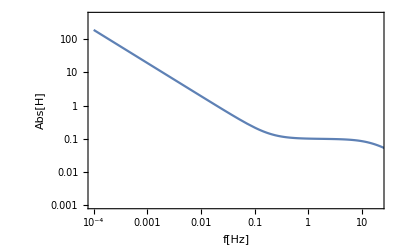

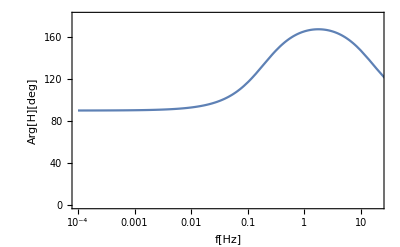

```mathematica
R13= 3.3M;(*doesn't affect anything*)
C7=15n; (*doesn't affect anything*)
C8=100u;
C6=10u;
R11=1k;
R10=82.0k;

H[ω_]:=-(1/(I ω C8)+para[R13,C7])/(para[1/(I ω C6),R10]+R11);

LogLogPlot[Abs[H[2π f]],{f,.0001,1k},PlotRange->{{10^-4,20},{.001,500}},Axes->False,Frame->True,FrameLabel->{"f[Hz]","Abs[H]"},LabelStyle->{Black,17}]

LogLinearPlot[Arg[H[2π f]]180/π,{f,.0001,1k},PlotRange->{{10^-4,20},{0,180}},Axes->False,Frame->True,FrameLabel->{"f[Hz]","Arg[H][deg]"},LabelStyle->{Black,17}]
```

```mathematica
slope is maintained no matter what...

increase C6 moves plateau up(preserves length of plateau)
decrease C8 increase gain by constant amt

increase R10--> extend plateau by extending lower freq side
decrease R11->extend plateau by extending high freq side
```

# original; 10, 10uF